```mathematica
Exit[]
```

```mathematica
Get["Quantica`Systems`"]
```

```mathematica
{T,V}=Systems`JeremyNormal[phi->1]
```

OptionValue::optnf: オプション名0はSystems`Private`JeremyNormalのデフォルトにはありません．

Set::setraw: 未加工オブジェクト0に割当てができません．

{Systems`Private`T$366,Systems`Private`V$366}

```mathematica
T[q,p]
```

1/2 (Cos[p]^2+Cos[q]^2) a1_.+(Cos[p]^2+Cos[q]^2)^2 a2_.

```mathematica
H[q_,p_]:=T[q,p]+V[q,p]
```

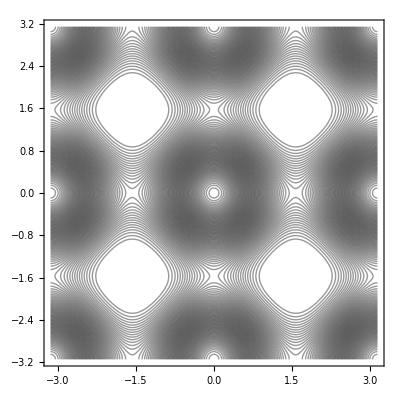

```mathematica
ContourPlot[H[q,p],{q,-Pi,Pi},{p,-Pi,Pi},Contours->80,ContourShading->None]
```